```mathematica
(***************************************)
(****Scalar field equaition*************)
(***************************************)
(***************************************)
(***************Background In case!****************)
(***************************************)
w=-0.9;
cs=10^-3;
H0=0.00022593979933110373;h=0.67556;
Omegab=0.022032/h/h;Omegacdm=0.12038/h/h;
Omegam=Omegab+Omegacdm;OmegaLambda=0.0;
Omegarad=9.16681 10^-5;Omegakessence=1.-Omegam-Omegarad;
Hubb[a_]:=H0 a √(Omegam a^-3+Omegarad  a^-4+OmegaLambda+Omegakessence a^(-3*(1+w)));
LogLogPlot[Hubb[a],{a,1./(1.+100),1}];
SetDirectory[NotebookDirectory[]];
Eq1II=3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]+cs^2 Ψ[τ]) +ζ'[τ]-3 cs^2 Φ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]- ζ[τ]+H[τ]piC[τ]-Ψ[τ];

Eq1I=Eq1II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
Eq2I=Eq2II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
a''[τ]=a[τ](H[τ]^2+H'[τ]);
a'[τ]=a[τ]H[τ];
H[τ_]:=Hubb[a[τ]];
(*Field equation in terms of scale factor!*)
Eq1:=Eq1I/.a[τ]:>a;
Eq2:=Eq2I/.a[τ]:>a;
```

```mathematica
(***************************************)
(***************IC read fromt the file***)
(***************************************)
(*Class file columns: # 1:k (h/Mpc) 2:d_kess_pi 3:t_kess_zeta 4:delta_fld 5:theta_fld 6:psi 7:delta_cdm 8:H_conf/H0 *)
data=Import["./Class_files/Class_kess_cs_e3_z100_newt_Gev.dat",{"Data",{All}}];

(*Making output file foe Gev field!*)
As=2.19 10^-9;
h=0.67556;
kp=0.05/h;
ns=0.96;
cs2=10^-6;
(*dataGevphiz100=Import["./256Ngrid_10kess_phi_prime_included/kess_pk_cs_e3_000_phi_z100.dat",{"Data",{All}}];*)
(*GevFieldz21=√(datapiGev21[[All,2]]/(As (datapiGev21[[All,1]]/kp)^(ns-1)));*)
a0=1./(1.+100.);
a1=1./(1.+10.);
Δa=0.00005; (*Sampling to solve ODE*)
Agrex=Table[Table[0,{aa,1,Floor[((a1-a0)/Δa)]+1},{num,1,3}],{k,1,Dimensions[data[[All,1]]][[1]]}];
Dimensions[Agrex](*k , a , pi[a], zeta[a]*)(*For each k we have a * 3 where a is the number of a sampling and 3 is the number of columns. a pi and pi' for  *)
(*Agrex[[4]] //MatrixForm*)

(***************************************)
(****For each k in IC file we need to solve th e ODE numerically!***************)
(***************************************)
kmax=Dimensions[data[[All,1]]][[1]];
amaxComun=Floor[((a1-a0)/Δa)]+1;
```

{199,1621,3}

```mathematica
For[kk=1,kk<kmax+1,kk++,
(*k is wavenumber in the eq
The IC is set for each wavenumber accordingly!
Also \Psi is set for each k accordingly in the loop which is assumed to be constant in matter dominated universe!*)
kwave=data[[kk,1]]*h; (*We multiply by h since the unit of k is 1/Mpc not h/Mpc! while in the file is k=[h/Mpc] *)
(*piC'[a0]==data[[kk,3]]/(Hubb[a0]a0) is IC for dπ/da*)
Ψ[τ]=data[[kk,6]];
Φ'[τ]=0;
(*Ψ=0;*)
(*Φprime must be provided in new variable a[tau]*)
(*Φprime=Gevphiprimez21[[kk]]Hubb[a0];*)
Sol=NDSolve[{Eq1==0,Eq2==0,piC[a0]==data[[kk,2]],ζ[a0]==data[[kk,3]]},{piC,ζ},{a,a0,a1}]; (*Note that for the initial value of π'[a0] it is not just data[[kk,3]]/(Hubb[a0]a0) since now it is the function of "a" which gets a new coefficient by changing the variable but not for ζ which is dimensionless*)
Agrex[[kk]][[All,1]]=Table[a,{a,a0,a1,Δa}];
(*Hubb[a]piC[a] is dimensionless field,  piC'[a]Hubb[a]a is dπ/dτ according to chain rule!*)
Agrex[[kk]][[All,{2,3}]]=Table[{Hubb[a]piC[a]/.Sol, ζ [a]/.Sol},{a,a0,a1,Δa}]; (*Hubb[a]piC[a] is a dimensionless variable and ζ [a]Hubb[a]a is to change in temrs of conformal time*)
]
Agrex[[3]][[{2,7},2]]//MatrixForm ;(*To check consistency!*)
(*K info is in the loaded file, and for each k we have the solution in time (pi, pi')!*)
(*Ψdata[[i,1]] is k lists! Agrex[[i]][[2,2]][[1]] is pi soluition for constant time!*)
MatSolz100=Table[{data[[k,1]],Abs[Agrex[[k]][[1,2]][[1]]],Abs[Agrex[[k]][[1,3]][[1]]]},{k,1,kmax}];
MatSolz10=Table[{data[[k,1]],Abs[Agrex[[k]][[amaxComun,2]][[1]]],Abs[Agrex[[k]][[amaxComun,3]][[1]]]},{k,1,kmax}]//N;
```

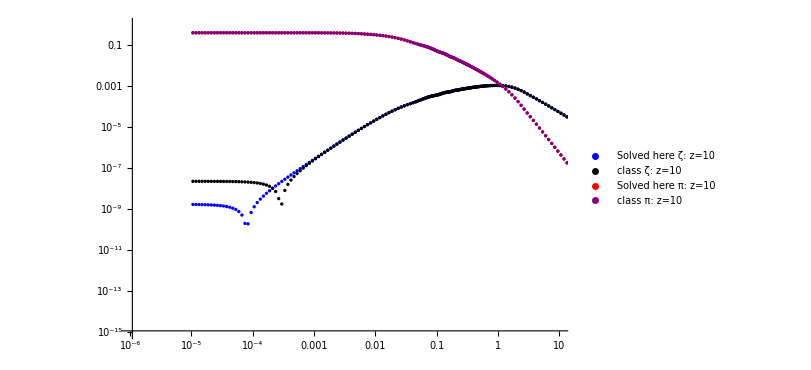

```mathematica
dataz10=
Import["./Class_files/Class_kess_cs_e3_z10_newt_Gev.dat",{"Data",{All}}];

(*Making π H for comparison in class*)
Classpiz100=Table[{data[[k,1]],Abs[data[[k,2]] Hubb[a0]]},{k,1,Dimensions[data][[1]]}]; 
Classpiz10=Table[{dataz10[[k,1]],Abs[dataz10[[k,2]] Hubb[a1]]},{k,1,Dimensions[dataz10][[1]]}];
Classzetaz100=Table[{data[[k,1]],Abs[data[[k,3]]]},{k,1,Dimensions[data][[1]]}]; 
Classzetaz10=Table[{dataz10[[k,1]],Abs[dataz10[[k,3]]]},{k,1,Dimensions[dataz10][[1]]}];
(*ClassMysolveRelDiffpiz10=Table[{dataz10[[k,1]],(dataz10[[k,2]] Hubb[a1]-Abs[Agrex[[k]][[amaxComun,2]][[1]]])/dataz10[[k,2]] Hubb[a1]},{k,1,Dimensions[data][[1]]}]; 
ClassMysolveRelDiffpivz10=Table[{dataz10[[k,1]],Abs[(dataz10[[k,3]] -Abs[Agrex[[k]][[amaxComun,3]][[1]]])]/dataz10[[k,3]]},{k,1,Dimensions[data][[1]]}]; *)

p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Solved here π: z=100"},ImageSize->400,PlotRange->{{10^-4,10},{10^-6,1}}];
p2=ListLogLogPlot[MatSolz10[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},ImageSize->400,PlotLegends->{"Solved here π: z=10"},PlotRange->{{10^-4,10},{10^-4,10}}];
pv1=ListLogLogPlot[MatSolz100[[All,{1,3}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Solved here ζ: z=100"},ImageSize->600,PlotRange->{{10^-6,10},{10^-9,1}}];
pv2=ListLogLogPlot[MatSolz10[[All,{1,3}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Solved here ζ: z=10"},ImageSize->600,PlotRange->{{10^-6,10},{10^-15,1}}];
(*pi class*)
piclassz100=ListLogLogPlot[Classpiz100[[All,{1,2}]],PlotStyle->{Orange,Line,PointSize[0.004]},PlotLegends->{"class π: z=100"},ImageSize->600];
piclassz10=ListLogLogPlot[Classpiz10[[All,{1,2}]],PlotStyle->{Purple,Line,PointSize[0.004]},PlotLegends->{"class π: z=10"},ImageSize->600];
(*zeta class*)zetaclassz100=ListLogLogPlot[Classzetaz100[[All,{1,2}]],PlotStyle->{Black,Line,PointSize[0.004]},PlotLegends->{"class ζ: z=100"},ImageSize->900,PlotRange->{{10^-6,5},{10^-9,1}}];
zetaclassz10=ListLogLogPlot[Classzetaz10[[All,{1,2}]],PlotStyle->{Black,Line,PointSize[0.004]},PlotLegends->{"class ζ: z=10"},ImageSize->600];
(*Show[p1,piclassz100];
Show[p2,piclassz10];*)
Show[pv2,zetaclassz10 ,p2,piclassz10]
```